```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"];
```

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

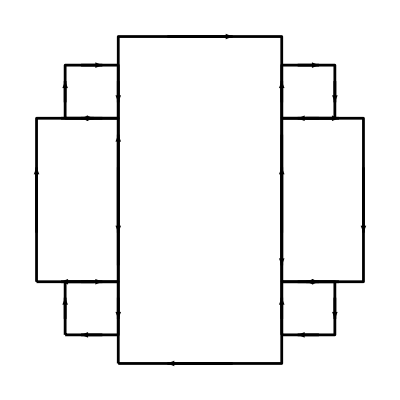

```mathematica
ClearAll[makeRect,makeArrows, drawOrientedRect, rect1, rect2, rect3, rect4, r, rectangles, orientedIntegralsFig2]
makeRect[bl_,w_,h_]:=With[{x=bl[[1]],y=bl[[2]]},{{x,y},{x,y+h},{x+w,y+h},{x+w,y},{x,y}}]

makeArrows[pts_,frac_]:=Module[{sides,p1,p2,vec,start,end},sides=Partition[pts,2,1];
Table[p1=side[[1]];p2=side[[2]];
vec=p2-p1;
start=p1+frac*vec;
end=p2-frac*vec;
{start,end},{side,sides}]]

drawOrientedRect[rect_,frac_,color_]:=Module[{arrows},arrows=makeArrows[rect,frac];
{color,Thickness[0.005],Line[rect],Arrowheads[0.06],Arrow/@arrows}]

(*Define rectangles*)
rect1=makeRect[{0,-1.5},2,4];
rect2=makeRect[{-1,-0.5},1,2];
rect3=makeRect[{2,-0.5},1,2];
r[p_] := makeRect[p, .65, .65]
rectangles = {rect1, rect2, rect3, 
r[{-.65, 1.5}],
r[{2.65-.65, 1.5}],
r[{-.65, 1.5-2.65}],
r[{2.65-.65, 1.5-2.65}]
};

(*Draw all with one line per rectangle*)
orientedIntegralsFig2 = Graphics[{drawOrientedRect[#,0.3,Black]&/@ rectangles},(*GridLines->Automatic,*)AspectRatio->1]
```

```mathematica
peeters`exportForLatex["orientedIntegralsFig2",orientedIntegralsFig2]
```

{orientedIntegralsFig2.eps,orientedIntegralsFig2pn.png}